# Data Analysis for Frequency Response

The analysis for each set-up is written after the plots for each set-up.

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v10.x, Version 1.95, 1/2016

Caltech Sophomore Physics Labs, Pasadena, CA

## Low-Q, Amplitude

Fitting the entire spectrum

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, Nonstandard -> True, DataFunction -> FreqResp]]
]
```

/home/ybadal/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph 6/Lab 1/frequency_sweep_all_low_q.dat

File comment header:

Sweep #00050	3:42:31 PM 1/16/2018
DAQ: PCI-6221; 16 bits; Timebase 80MHz; Max ADC 250kHz, ETS 20MHz
Resolutions: Src ADC 0.0uV; Resp ADC 0.0uV
Max ADC V: Src 0.0V; Resp 0.0V; Repeat 3; Settle 0.080sec
Waveform Sampling: 25.0 cycles @ 7.5 samples/cycle; no preaveraging
Signal Generator: Agilent Technologies 33220A Waveform Generator
Generator:        	                    	                    	Input:              	                    	                    	                    	Response:
Freq (Hz)         	Amplitude (V)       	Offset (V)          	Amplitude (V)       	sig Amplitude       	Phase (deg)         	sig Phase           	Amplitude (V)       	sig Amplitude       	Phase (deg)         	sig Phase

Read 600 data points.

```mathematica
SecondOrderLPFilterFit[]
```

n = 600

y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b

a= 
0.995195 | b= 
-0.00325229 | 
σ_a= 
0.000207488 | σ_b= 
0.000584628 | 
ω_0= 
15584.9 | Q= 
17.556 | 
σ_ω_0= 
0.0758709 | σ_Q= 
0.004379 | Std. deviation= 
0.0110044

Fit of (x,y±σ_y)

a= 
0.996302 | b= 
-0.00534373 | 
σ_a= 
0.0000174574 | σ_b= 
3.65233×10^-7 | 
ω_0= 
15583.4 | Q= 
17.5407 | 
σ_ω_0= 
0.0305951 | σ_Q= 
0.000906029 | χ^2/(n-4)= 
300.727

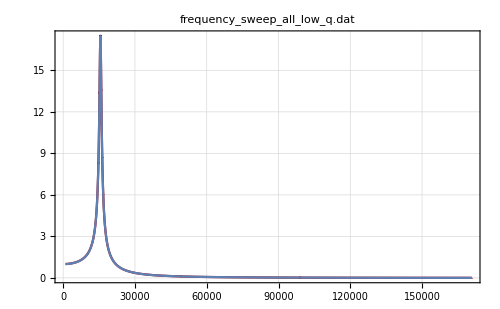
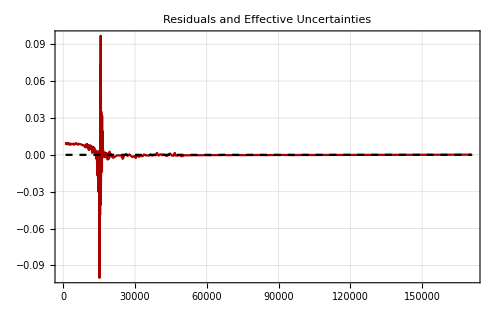
-Graphics-
-Graphics-
y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b
a= 
0.996302 | b= 
-0.00534373 | 
σ_a= 
0.0000174574 | σ_b= 
3.65233×10^-7 | 
ω_0= 
15583.4 | Q= 
17.5407 | 
σ_ω_0= 
0.0305951 | σ_Q= 
0.000906029 | χ^2/(n-4)= 
300.727

```mathematica
LinearDifferencePlot[]
```

Fitting close to the peak

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{13400.,17900.}

n= 187

413 points removed.

```mathematica
SecondOrderLPFilterFit[]
```

n = 187

y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b

a= 
0.99328 | b= 
0.00836817 | 
σ_a= 
0.00112348 | σ_b= 
0.00807622 | 
ω_0= 
15584.9 | Q= 
17.5811 | 
σ_ω_0= 
0.129494 | σ_Q= 
0.0144517 | Std. deviation= 
0.0186891

Fit of (x,y±σ_y)

a= 
0.993382 | b= 
0.00664672 | 
σ_a= 
0.000160115 | σ_b= 
0.000800296 | 
ω_0= 
15584.8 | Q= 
17.5928 | 
σ_ω_0= 
0.0336276 | σ_Q= 
0.00275452 | χ^2/(n-4)= 
6.90579

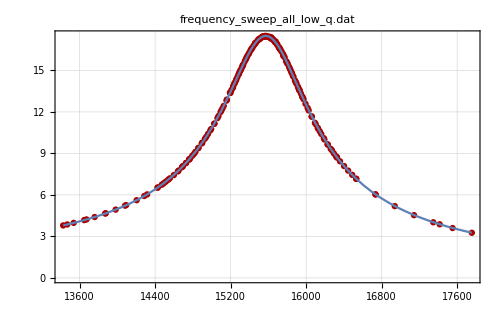
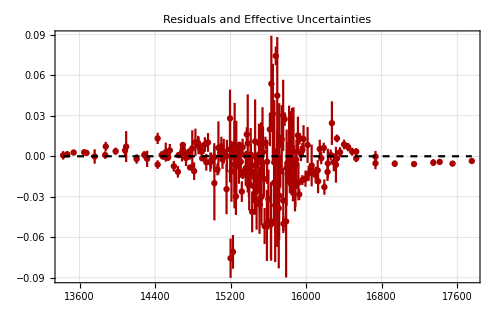
-Graphics-
-Graphics-
y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b
a= 
0.993382 | b= 
0.00664672 | 
σ_a= 
0.000160115 | σ_b= 
0.000800296 | 
ω_0= 
15584.8 | Q= 
17.5928 | 
σ_ω_0= 
0.0336276 | σ_Q= 
0.00275452 | χ^2/(n-4)= 
6.90579

```mathematica
LinearDifferencePlot[]
```

Fitting the entire spectrum on a Log-Log scale

```mathematica
SecondOrderLPFilterFit[]
```

n = 600

y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b

a= 
0.995195 | b= 
-0.00325229 | 
σ_a= 
0.000207488 | σ_b= 
0.000584628 | 
ω_0= 
15584.9 | Q= 
17.556 | 
σ_ω_0= 
0.0758709 | σ_Q= 
0.004379 | Std. deviation= 
0.0110044

Fit of (x,y±σ_y)

a= 
0.996302 | b= 
-0.00534373 | 
σ_a= 
0.0000174574 | σ_b= 
3.65233×10^-7 | 
ω_0= 
15583.4 | Q= 
17.5407 | 
σ_ω_0= 
0.0305951 | σ_Q= 
0.000906029 | χ^2/(n-4)= 
300.727

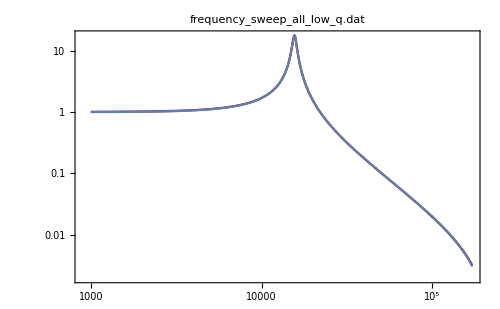
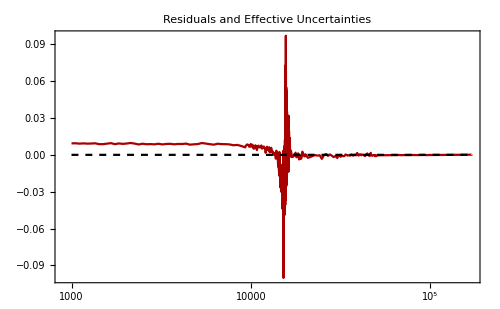
-Graphics-
-Graphics-
y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b
a= 
0.996302 | b= 
-0.00534373 | 
σ_a= 
0.0000174574 | σ_b= 
3.65233×10^-7 | 
ω_0= 
15583.4 | Q= 
17.5407 | 
σ_ω_0= 
0.0305951 | σ_Q= 
0.000906029 | χ^2/(n-4)= 
300.727

```mathematica
LogLogDifferencePlot[]
```

Analysis for frequency response, low-Q (gain)

We observe that fitting the entire spectrum results in a large (χ̃)^2 value (~300) whereas by fitting close the resonance peak we obtain a much smaller (χ̃)^2 value of 6.9. This indicates that the theory may be ill-suited to model regimes far away from the resonant frequency of the oscillator. 

In fact, by fitting and plotting the entire spectrum on a Log-Log scale, we can observe a feature that indicates that this is indeed the case: the theory predicts that gain decreases as 1/ω^2 for ω >> ω_0, If that were the case, the Log-Log plot would show a linear decrease at the rightmost tail of the frequency spectrum. Indeed, this is the case for a large range of frequencies above the resonant frequency, but at high enough frequencies the plot shows non-linear features, indicating disagreement with the theory at high enough frequencies and explaining the discrepancies in the (χ̃)^2 values obtained when fitting the entire spectrum and only the peak.

From the fit near the peak, we can also provide the following estimates for:

ω_0 = 97922.2 ± 0.2 rad sec^-1
Q = 17.593 ± 0.003

## Low-Q, Phase

We observe that it is not possible to fit the data obtained because of the abnormal behavior at the higher frequencies. We suspect that this is a signal-to-noise ratio issue and discard that portion of the data before attemtping a fit.

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, Nonstandard -> True, DataFunction -> FreqResp]]
]
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, Nonstandard -> True, DataFunction -> FreqResp]]
]
```

/home/ybadal/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph 6/Lab 1/frequency_sweep_all_low_q.dat

File comment header:

Sweep #00050	3:42:31 PM 1/16/2018
DAQ: PCI-6221; 16 bits; Timebase 80MHz; Max ADC 250kHz, ETS 20MHz
Resolutions: Src ADC 0.0uV; Resp ADC 0.0uV
Max ADC V: Src 0.0V; Resp 0.0V; Repeat 3; Settle 0.080sec
Waveform Sampling: 25.0 cycles @ 7.5 samples/cycle; no preaveraging
Signal Generator: Agilent Technologies 33220A Waveform Generator
Generator:        	                    	                    	Input:              	                    	                    	                    	Response:
Freq (Hz)         	Amplitude (V)       	Offset (V)          	Amplitude (V)       	sig Amplitude       	Phase (deg)         	sig Phase           	Amplitude (V)       	sig Amplitude       	Phase (deg)         	sig Phase

Read 600 data points.

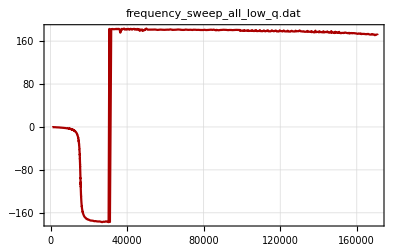

Fitting the entire (remaining) spectrum

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{1500.,25700.}

n= 306

```mathematica
ResonancePhaseDegreesCFit[]
```

n = 306

y(ω) = TraditionalForm`θ_0 - tan^-1(Q\ (ω/ω_0 - ω_0/ω))

Fit of (x,y)  (unweighted)

Calculating sigt

ω_0= 
15585.5 | θ_0= 
-89.7018 | Q= 
17.5499 | 
σ_ω_0= 
0.262258 | σ_θ_0= 
0.0167341 | σ_Q= 
0.0123042 | Std. deviation= 
0.212345

Fit of (x,y±σ_y)

Calculating sigt

ω_0= 
15585.2 | θ_0= 
-89.8168 | Q= 
17.5525 | 
σ_ω_0= 
0.117487 | σ_θ_0= 
0.00549419 | σ_Q= 
0.00642849 | χ^2/(n-3)= 
6.29228

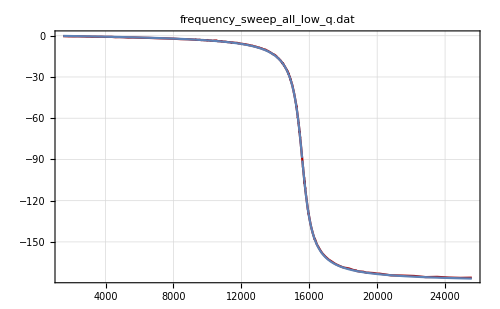
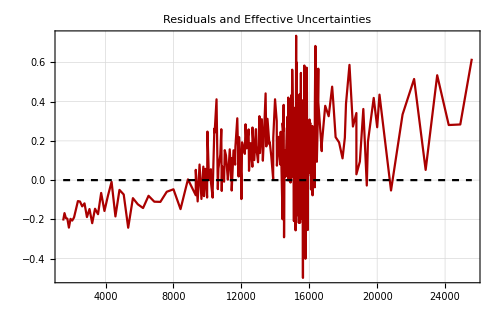
-Graphics-
-Graphics-
y(ω) = TraditionalForm`θ_0 - tan^-1(Q\ (ω/ω_0 - ω_0/ω))
ω_0= 
15585.2 | θ_0= 
-89.8168 | Q= 
17.5525 | 
σ_ω_0= 
0.117487 | σ_θ_0= 
0.00549419 | σ_Q= 
0.00642849 | χ^2/(n-3)= 
6.29228

```mathematica
LinearDifferencePlot[]
```

Fitting close to resonance

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{14160.,17160.}

n= 172

134 points removed.

```mathematica
ResonancePhaseDegreesCFit[]
```

n = 172

y(ω) = TraditionalForm`θ_0 - tan^-1(Q\ (ω/ω_0 - ω_0/ω))

Fit of (x,y)  (unweighted)

Calculating sigt

ω_0= 
15584.3 | θ_0= 
-89.5837 | Q= 
17.5498 | 
σ_ω_0= 
0.433882 | σ_θ_0= 
0.0367837 | σ_Q= 
0.0128978 | Std. deviation= 
0.215661

Fit of (x,y±σ_y)

Calculating sigt

ω_0= 
15581.8 | θ_0= 
-89.5 | Q= 
17.5277 | 
σ_ω_0= 
0.212342 | σ_θ_0= 
0.0175779 | σ_Q= 
0.00679529 | χ^2/(n-3)= 
4.92819

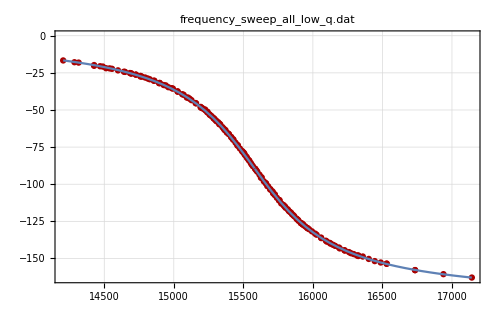
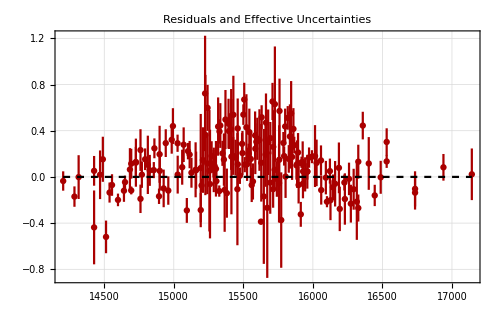
-Graphics-
-Graphics-
y(ω) = TraditionalForm`θ_0 - tan^-1(Q\ (ω/ω_0 - ω_0/ω))
ω_0= 
15581.8 | θ_0= 
-89.5 | Q= 
17.5277 | 
σ_ω_0= 
0.212342 | σ_θ_0= 
0.0175779 | σ_Q= 
0.00679529 | χ^2/(n-3)= 
4.92819

```mathematica
LinearDifferencePlot[]
```

Analysis for frequency spectrum, low-Q (Phase)

This time, our preliminary fit does not have such a bad (χ̃)^2 value at 6.9. We suspect that this is because the features indicating significant discrepancies with the theory would have occurred in the portion of the data removed due to signal-to-noise ratio issues. 

Nevertheless, the (χ̃)^2 is still improved to 4.9 by fitting around the resonant frequency, indicating that the theory is indeed most adequate at describing the system near the resonant frequency, and our measurements start to disagree with the system as we move away from that region. We can use the fit around the resonance to estimate:

ω_0 = 97903.2 ± 1.3 rad sec^-1
Q = 17.528 ± 0.007

## High-Q, Gain

Fitting the entire spectrum

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, Nonstandard -> True, DataFunction -> FreqResp]]
]
```

/home/ybadal/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph 6/Lab 1/frequency_sweep_all.dat

File comment header:

Sweep #00077	3:58:58 PM 1/16/2018
DAQ: PCI-6221; 16 bits; Timebase 80MHz; Max ADC 250kHz, ETS 20MHz
Resolutions: Src ADC 0.0uV; Resp ADC 0.0uV
Max ADC V: Src 0.0V; Resp 0.0V; Repeat 3; Settle 0.080sec
Waveform Sampling: 25.0 cycles @ 7.5 samples/cycle; no preaveraging
Signal Generator: Agilent Technologies 33220A Waveform Generator
Generator:        	                    	                    	Input:              	                    	                    	                    	Response:
Freq (Hz)         	Amplitude (V)       	Offset (V)          	Amplitude (V)       	sig Amplitude       	Phase (deg)         	sig Phase           	Amplitude (V)       	sig Amplitude       	Phase (deg)         	sig Phase

Read 600 data points.

```mathematica
SecondOrderLPFilterFit[]
```

n = 600

y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b

a= 
0.994224 | b= 
0.000475449 | 
σ_a= 
0.000502716 | σ_b= 
0.0103124 | 
ω_0= 
15582.4 | Q= 
141.944 | 
σ_ω_0= 
0.0240391 | σ_Q= 
0.0875712 | Std. deviation= 
0.206897

Fit of (x,y±σ_y)

a= 
0.994884 | b= 
-0.00535998 | 
σ_a= 
7.70704×10^-6 | σ_b= 
3.3008×10^-7 | 
ω_0= 
15582.9 | Q= 
141.605 | 
σ_ω_0= 
0.0059371 | σ_Q= 
0.0329822 | χ^2/(n-4)= 
935.739

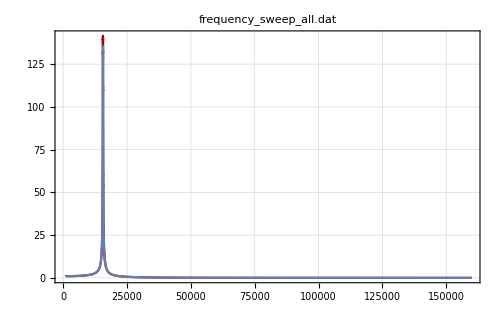
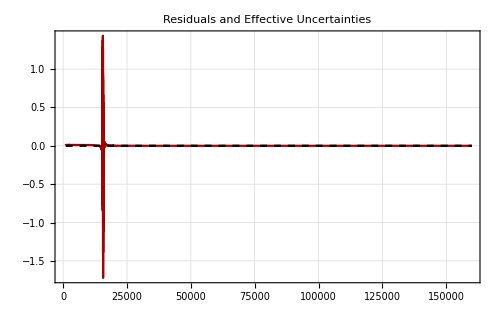
-Graphics-
-Graphics-
y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b
a= 
0.994884 | b= 
-0.00535998 | 
σ_a= 
7.70704×10^-6 | σ_b= 
3.3008×10^-7 | 
ω_0= 
15582.9 | Q= 
141.605 | 
σ_ω_0= 
0.0059371 | σ_Q= 
0.0329822 | χ^2/(n-4)= 
935.739

```mathematica
LinearDifferencePlot[]
```

Fitting the entire spectrum on a Log-Log scale

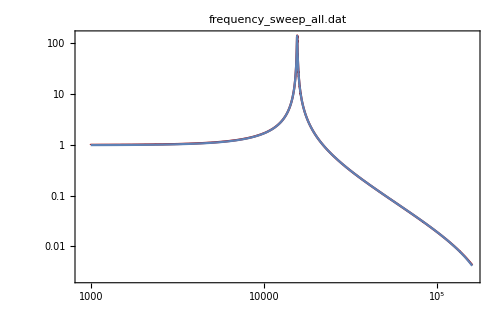
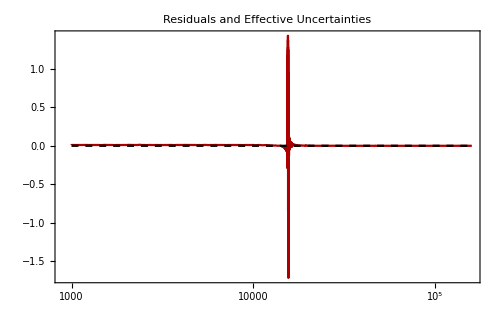
-Graphics-
-Graphics-
y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b
a= 
0.994884 | b= 
-0.00535998 | 
σ_a= 
7.70704×10^-6 | σ_b= 
3.3008×10^-7 | 
ω_0= 
15582.9 | Q= 
141.605 | 
σ_ω_0= 
0.0059371 | σ_Q= 
0.0329822 | χ^2/(n-4)= 
935.739

```mathematica
LogLogDifferencePlot[]
```

Fitting around the resonance peak

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{14300.,17000.}

n= 216

384 points removed.

```mathematica
SecondOrderLPFilterFit[]
```

n = 216

y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b

a= 
0.993703 | b= 
0.0259335 | 
σ_a= 
0.00148526 | σ_b= 
0.0628804 | 
ω_0= 
15582.4 | Q= 
141.999 | 
σ_ω_0= 
0.0401957 | σ_Q= 
0.195078 | Std. deviation= 
0.346695

Fit of (x,y±σ_y)

a= 
0.993245 | b= 
0.00995104 | 
σ_a= 
0.0000667406 | σ_b= 
0.000932331 | 
ω_0= 
15582.9 | Q= 
142.492 | 
σ_ω_0= 
0.0100365 | σ_Q= 
0.037444 | χ^2/(n-4)= 
34.9055

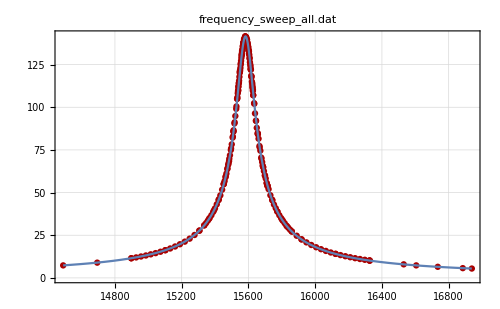
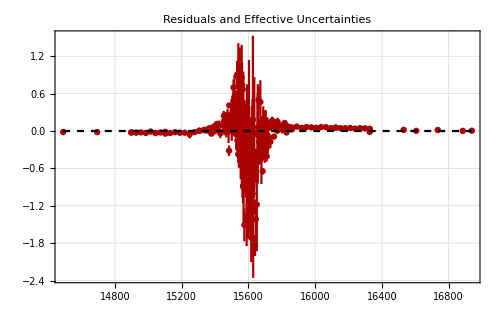
-Graphics-
-Graphics-
y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b
a= 
0.993245 | b= 
0.00995104 | 
σ_a= 
0.0000667406 | σ_b= 
0.000932331 | 
ω_0= 
15582.9 | Q= 
142.492 | 
σ_ω_0= 
0.0100365 | σ_Q= 
0.037444 | χ^2/(n-4)= 
34.9055

```mathematica
LinearDifferencePlot[]
```

Fitting closer to the resonance peak

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{15344.,15847.}

n= 166

50 points removed.

```mathematica
SecondOrderLPFilterFit[]
```

n = 166

y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b

a= 
0.992731 | b= 
0.0829224 | 
σ_a= 
0.00311705 | σ_b= 
0.167879 | 
ω_0= 
15582.4 | Q= 
142.089 | 
σ_ω_0= 
0.0460186 | σ_Q= 
0.330159 | Std. deviation= 
0.395299

Fit of (x,y±σ_y)

a= 
0.997565 | b= 
-0.139288 | 
σ_a= 
0.00038813 | σ_b= 
0.0120069 | 
ω_0= 
15582.5 | Q= 
141.584 | 
σ_ω_0= 
0.0131459 | σ_Q= 
0.0720923 | χ^2/(n-4)= 
9.27254

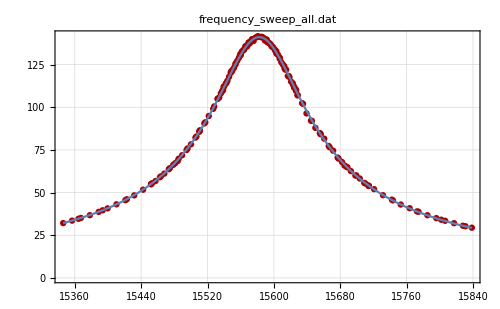
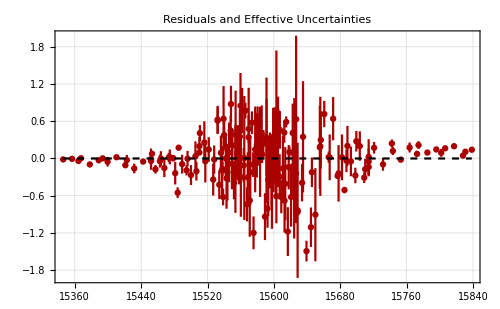
-Graphics-
-Graphics-
y(ω) = a ω_0 2/√(ω^ 2 - ω_0 2)^2 + (ω_0 ω/Q)^2 + b
a= 
0.997565 | b= 
-0.139288 | 
σ_a= 
0.00038813 | σ_b= 
0.0120069 | 
ω_0= 
15582.5 | Q= 
141.584 | 
σ_ω_0= 
0.0131459 | σ_Q= 
0.0720923 | χ^2/(n-4)= 
9.27254

```mathematica
LinearDifferencePlot[]
```

Analysis for frequency spectrum, high-Q (Gain)

We observe that fitting the entire spectrum results in an even larger (χ̃)^2 value (~935) than for fitting the entire spectrum in the low-Q case (~300). We also observe that we need to fit much closer to the resonance peak in order to obtain a reasonable fit and (χ̃)^2 value. By fitting close enough to the resonance peak, we reduce the (χ̃)^2 value to 9.2. This indicates that the theory may be ill-suited to model regimes far away from the resonant frequency of the oscillator as in the low-Q case, and furthermore that in the high-Q case the theory is more sensitive to how close to the resonance peak it is applied to (i.e. the theory is adequate to model an even smaller regime for a high-Q system than for a low-Q system).

In fact, by fitting and plotting the entire spectrum on a Log-Log scale, we can observe the same feature as before that indicates that this is indeed the case: the theory predicts that gain decreases as 1/ω^2 for ω >> ω_0, If that were the case, the Log-Log plot would show a linear decrease at the rightmost tail of the frequency spectrum. Indeed, this is the case for a large range of frequencies above the resonant frequency, but at high enough frequencies the plot shows non-linear features, indicating disagreement with the theory at high enough frequencies and explaining the discrepancies in the (χ̃)^2 values obtained when fitting the entire spectrum and only the peak. Furthermore, the Log-Log plot behaves non-linearly w.r.t frequency earlier in the high-Q case than in the low-Q case, explaining the higher sensitivity of the model for high-Q.

We can use the fit around the resonance to estimate:

ω_0 = 97907.99 ± 0.08 rad sec^-1
Q = 141.58 ± 0.07

## High-Q, Phase

We have the same issue here as we had before: possibly due to signal-to-noise ratio issues, the data behaves abnormally at higher frequencies and cannot be used for a fit. Therefore we discard the abnormal region of the data before attempting a fit.

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, Nonstandard -> True, DataFunction -> FreqResp]]
]
```

/home/ybadal/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph 6/Lab 1/frequency_sweep_all.dat

File comment header:

Sweep #00077	3:58:58 PM 1/16/2018
DAQ: PCI-6221; 16 bits; Timebase 80MHz; Max ADC 250kHz, ETS 20MHz
Resolutions: Src ADC 0.0uV; Resp ADC 0.0uV
Max ADC V: Src 0.0V; Resp 0.0V; Repeat 3; Settle 0.080sec
Waveform Sampling: 25.0 cycles @ 7.5 samples/cycle; no preaveraging
Signal Generator: Agilent Technologies 33220A Waveform Generator
Generator:        	                    	                    	Input:              	                    	                    	                    	Response:
Freq (Hz)         	Amplitude (V)       	Offset (V)          	Amplitude (V)       	sig Amplitude       	Phase (deg)         	sig Phase           	Amplitude (V)       	sig Amplitude       	Phase (deg)         	sig Phase

Read 600 data points.

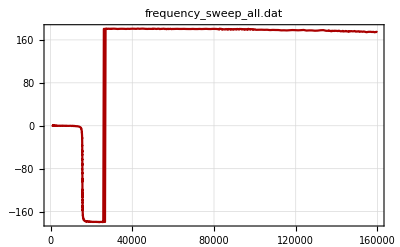

Fitting the entire (remaining) spectrum

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{4700.,24300.}

n= 316

284 points removed.

```mathematica
ResonancePhaseDegreesCFit[]
```

n = 316

y(ω) = TraditionalForm`θ_0 - tan^-1(Q\ (ω/ω_0 - ω_0/ω))

Fit of (x,y)  (unweighted)

Calculating sigt

ω_0= 
15582.5 | θ_0= 
-89.8077 | Q= 
142.214 | 
σ_ω_0= 
0.0955952 | σ_θ_0= 
0.0439559 | σ_Q= 
0.311 | Std. deviation= 
0.615926

Fit of (x,y±σ_y)

Calculating sigt

ω_0= 
15582.9 | θ_0= 
-89.871 | Q= 
142.232 | 
σ_ω_0= 
0.022245 | σ_θ_0= 
0.00420978 | σ_Q= 
0.103762 | χ^2/(n-3)= 
5.23857

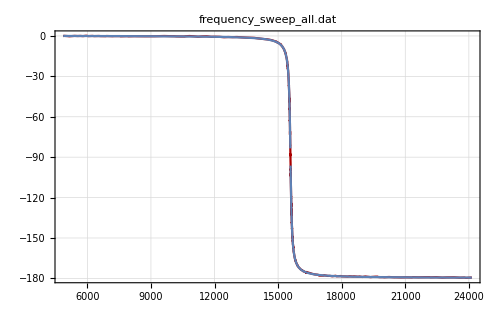
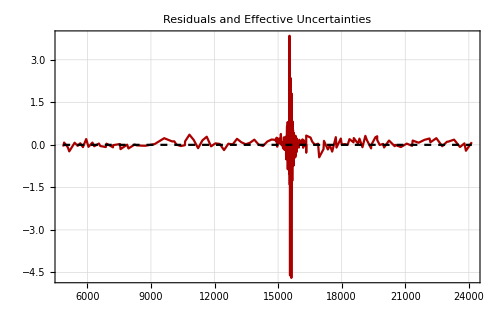
-Graphics-
-Graphics-
y(ω) = TraditionalForm`θ_0 - tan^-1(Q\ (ω/ω_0 - ω_0/ω))
ω_0= 
15582.9 | θ_0= 
-89.871 | Q= 
142.232 | 
σ_ω_0= 
0.022245 | σ_θ_0= 
0.00420978 | σ_Q= 
0.103762 | χ^2/(n-3)= 
5.23857

```mathematica
LinearDifferencePlot[]
```

Fitting close to the resonance frequency

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{14570.,16250.}

n= 205

111 points removed.

```mathematica
ResonancePhaseDegreesCFit[]
```

n = 205

y(ω) = TraditionalForm`θ_0 - tan^-1(Q\ (ω/ω_0 - ω_0/ω))

Fit of (x,y)  (unweighted)

Calculating sigt

ω_0= 
15582.5 | θ_0= 
-89.7781 | Q= 
142.212 | 
σ_ω_0= 
0.143543 | σ_θ_0= 
0.081758 | σ_Q= 
0.384136 | Std. deviation= 
0.759381

Fit of (x,y±σ_y)

Calculating sigt

ω_0= 
15582.8 | θ_0= 
-89.8086 | Q= 
142.286 | 
σ_ω_0= 
0.0279375 | σ_θ_0= 
0.0141483 | σ_Q= 
0.104738 | χ^2/(n-3)= 
5.32816

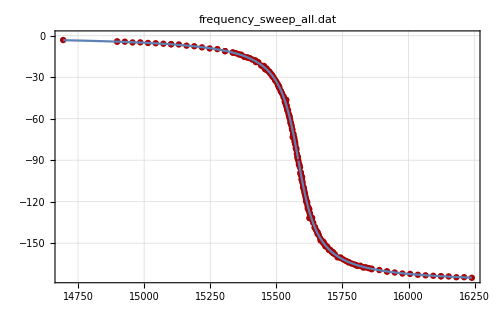
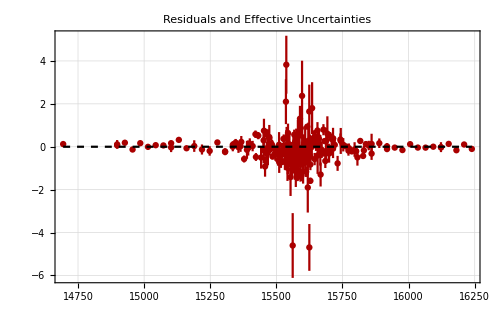
-Graphics-
-Graphics-
y(ω) = TraditionalForm`θ_0 - tan^-1(Q\ (ω/ω_0 - ω_0/ω))
ω_0= 
15582.8 | θ_0= 
-89.8086 | Q= 
142.286 | 
σ_ω_0= 
0.0279375 | σ_θ_0= 
0.0141483 | σ_Q= 
0.104738 | χ^2/(n-3)= 
5.32816

```mathematica
LinearDifferencePlot[]
```

Again, our preliminary fit has a surprisingly good (χ̃)^2 value (~5.23) - in fact, it has a slightly lower value than the fit around resonance (~5.32)! We suspect that this is because the features indicating significant discrepancies with the theory would have occurred in the portion of the data removed due to signal-to-noise ratio issues, and possibly because the data points near resonance are too sparse. 

Nevertheless, the similar (χ̃)^2 for the entire fit and for the fit around resonance indicate that for high-Q systems, the theory is much less brittle w.r.t the region in the frequency domain being considered than it is for analyzing the gain w.r.t frequency (i.e. the theory is adequate to model the phase for a larger range of frequencies in the high-Q case). This is the opposite of what we found regarding using the theory to model the gain of the system.

We can use our fit around the resonance to estimate:

ω_0 = 97909.8 ± 0.2 rad sec^-1
Q = 142.3 ± 0.1

## Conclusion

We observe a discrepancy of around 36 rad sec^-1 between our calculated value and the value we obtained experimentally in both the high-Q and low-Q cases. We use the experimental ω_0 to find C and Q:

```mathematica
l=10.13*10^-3;
Subscript[ω, 0]=2π*15582.83;
c=1/(Subscript[ω, 0]^2 l)
```

1.02977×10^-8

Therefore, the capacitance must be C = 10.29 nF. Similarly,

```mathematica
q=142.29;
r=1/q Sqrt[l/c]
```

6.97046

Therefore, R = 6.98 Ω for the high-Q case. This means R_L=6.98 Ω, which is much higher than the 1.31 Ω DC resistance of the inductor.